```mathematica
Nruns=20;
runs={};

colors = discreteColors[Nruns+1];
runs$plot={};

Do[(
log=NotebookDirectory[]<>"log_"<>ToString[run]<>".txt";
data=ReadList[log,{Number, Number}];
color=colors[[run+2]];
AppendTo[runs,data];
AppendTo[runs$plot,
ListPlot[data,PlotStyle->{Lighter[color,0.7],PointSize[0.005]}]
];
),{run,Range[0,Nruns-1]}];
```

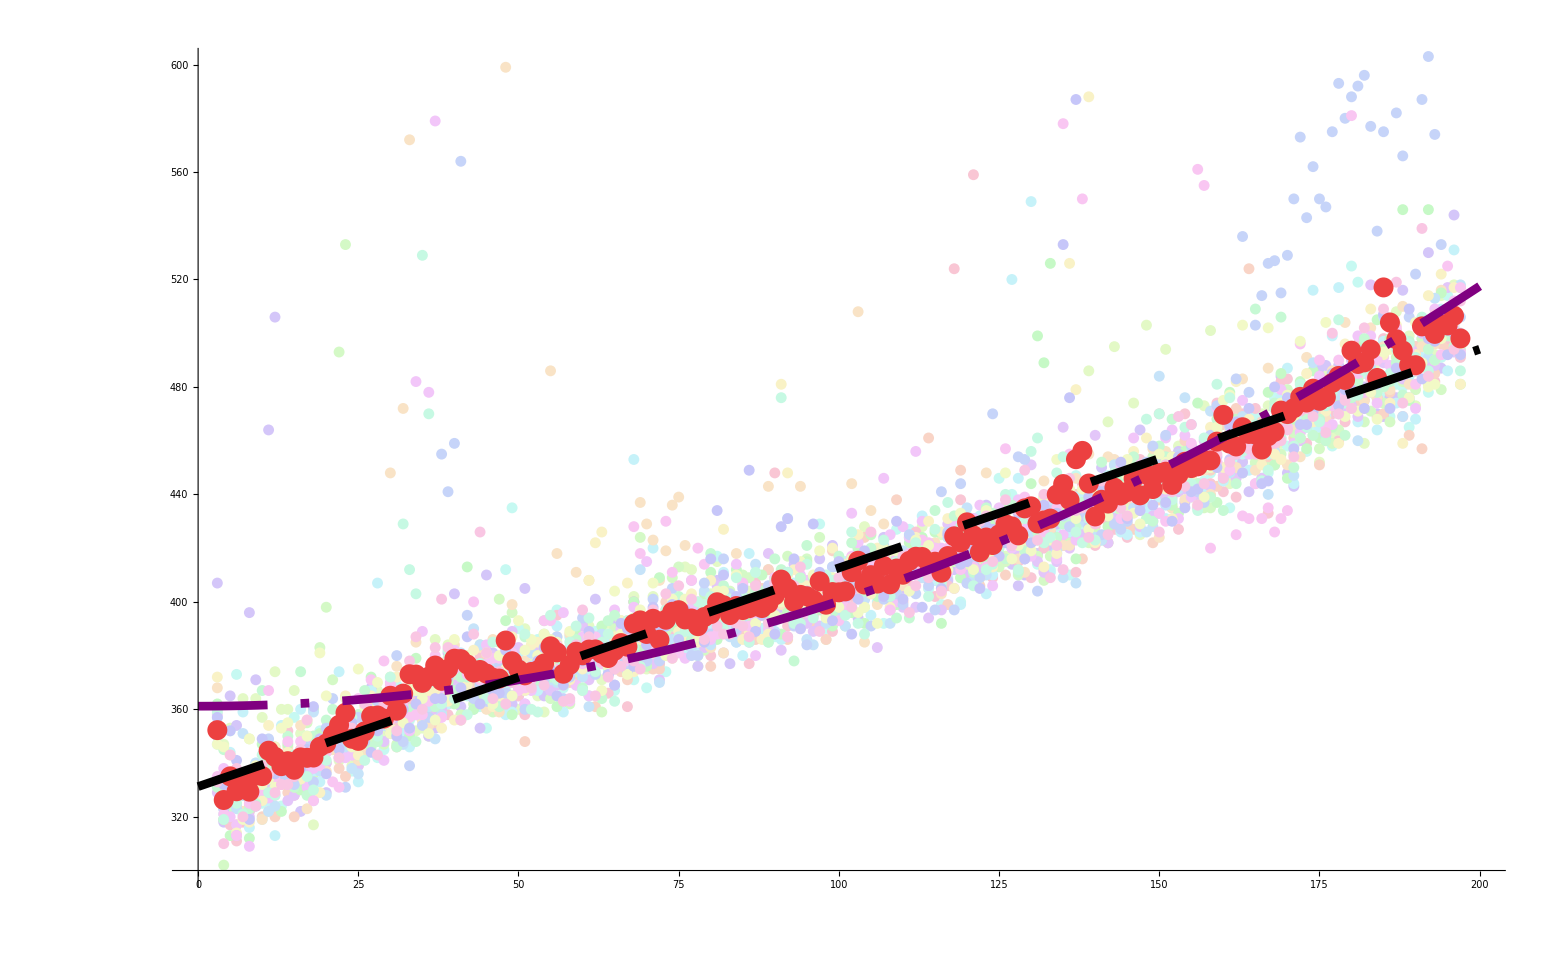

```mathematica
runs$avg=Mean[runs];

linear = Fit[runs$avg, {1,x},x];
square = Fit[runs$avg, {1,x^2},x];

result=Show[
runs$plot,
ListPlot[runs$avg,PlotStyle->colors[[1]],AxesOrigin->{0,300}],
Plot[square,{x,0,200},PlotStyle->{Thickness[0.004],Purple,Dashing[{0.04,0.0152, 0.004, 0.0152}]}],
Plot[linear,{x,0,200},PlotStyle->{Thickness[0.004],Black, Dashing[{0.04,0.03}]}],
PlotRange->{{0,200},{300,600}},AxesOrigin->{0,300}
]
```